```mathematica
Clear["Global`*"]
Ung=200*10^9;
ν=0.3;
DD={{λ+2*μ,λ,0},{λ,λ+2μ,0},{0,0,μ}};
λ=ν*Ung/(1+ν)/(1-2*ν);
μ=Ung/2/(1+ν);
ρ=7850;
MatrixForm@DD;
ϵ0={{α*dt},{α*dt},{0}};
α=13*10^-15;
dt=10;
```

```mathematica
a=0.5;
a1=2;
a2=3;
ζ=N[24a/100];
Reg1=Parallelogram[{3*a,2*a},{{0,a1*a},{3*a,0}}];
Reg2=Parallelogram[{3*a,2*a},{{0,a1*a},{-3*a,0}}];
Reg3=Parallelogram[{3*a,2*a},{{0,-a1*a},{3*a,0}}];
Reg4=Parallelogram[{3*a,2*a},{{0,-a1*a},{-3*a,0}}];
(*Reg5=Disk[{3a,2a},a/2];*)
Reg1234=RegionUnion[Reg1,Reg2,Reg3,Reg4];
(*ℛ=RegionDifference[Reg1234,Reg5];*)
Reg=DiscretizeRegion[Reg1234,MeshCellLabel->{0->"Index"},MaxCellMeasure->.01]
MeshRegionQ[Reg];
Coord=MeshCoordinates[Reg];
Polys=MeshCells[Reg,2];
For[i=1,i≤Length[Polys],i++,rho[i]=1];
NOP=30;
δe=Table[0,{i,1,NOP}];
♌=3000;
EnergyCriteria=Table[0,{i,1,NOP}];(*Множитель Лагранжа*)
```

-Graphics-

```mathematica
(*For[Iterator=1,Iterator≤2,Iterator++,*)
```

```mathematica
For[OP=1,OP≤NOP,OP++,
Width=Table[0.001*rho[i],{i,1,Length[Polys]}];
Length[StifnessMatrix];
(*Площадь i элемента*)
S[i_]:=0.5*((Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]])-(Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,3]],2]]));
(*Коэффициенты функций формы i элемента*)
(*i*)
ai[i_]:=Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,2]],2]];
bi[i_]:=Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]];
ci[i_]:=Coord[[Polys[[i,1,3]],1]]-Coord[[Polys[[i,1,2]],1]];
(*j*)
aj[i_]:=Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,3]],2]];
bj[i_]:=Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,1]],2]];
cj[i_]:=Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]];
(*m*)
am[i_]:=Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,1]],2]];
bm[i_]:=Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,2]],2]];
cm[i_]:=Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,1]],1]];
(*Функции формы*)
Ni[i_]:=1/(2S[i])*(ai[i]+bi[i]*x+ci[i]*y);
Nj[i_]:=1/(2S[i])*(aj[i]+bj[i]*x+cj[i]*y);
Nm[i_]:=1/(2S[i])*(am[i]+bm[i]*x+cm[i]*y);
(*Задание матрицы B*)
B[i_]:={
{D[Ni[i],x],0,D[Nj[i],x],0,D[Nm[i],x],0},
{0,D[Ni[i],y],0,D[D[Nj[i],y]],0,D[D[Nm[i],y]]},
{D[Ni[i],y],D[Ni[i],x],D[Nj[i],y],D[Nj[i],x],D[Nm[i],y],D[Nm[i],x]}
};
MatrixForm@B[86];
PreIntB[i_]:=Transpose[B[i]].DD.B[i];
Ke[i_]:=PreIntB[i]*S[i]*Width[[i]];
(*Критерий Сильвестра и симметричность матрицы соблюдены*)
StifnessMatrix=Table[0,{i,1,Length[Coord]*2},{j,1,Length[Coord]*2}];
Length[Polys];
For[b=1,b≤Length[Polys],b++,
NUM={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
For[p=1,p<=6,p++,
For[g=1,g<=6,g++,
StifnessMatrix[[NUM[[p]],NUM[[g]]]]=Ke[b][[p,g]]+StifnessMatrix[[NUM[[p]],NUM[[g]]]];
];
];
];
(*Формирование силовых факторов и перемещений*)
Displacement=Table[δ[i],{i,1,Length[Coord]*2}];
Force=Table[f[i],{i,1,Length[Coord]*2}];
(*Сосредоточенная нагрузка*)
k1=45;
k2=35;
For[i=1,i≤Length[Coord]*2,i++,
f[i]=0;
];
f[k1*2]=-100000*9.8;
f[k2*2]=-100000*9.8*0;
(*Массовые силы(Сила тяжести),Температурная нагрузка*)
PreIntϵ[i_]:=Transpose[B[i]].DD.ϵ0;
For[b=1,b≤Length[Polys],b++,
NUM={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
FMass=-S[b]*Width[[b]]*ρ*9.8*0;
TF=PreIntϵ[b]*10000000*0;
f[NUM[[1]]]=f[NUM[[1]]]+TF[[1]];
f[NUM[[2]]]=f[NUM[[2]]]+FMass/3+TF[[2]];
f[NUM[[3]]]=f[NUM[[3]]]+TF[[3]];
f[NUM[[4]]]=f[NUM[[4]]]+FMass/3+TF[[4]];
f[NUM[[5]]]=f[NUM[[5]]]+TF[[5]];
f[NUM[[6]]]=f[NUM[[6]]]+FMass/3+TF[[6]];
];
(*Распределенные нагрузки*)
N1=8;
N2=54;
Q=-5000000000*0;
L=1;
Incr=0;
For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],Incr=Incr+1]
];
FPress=Q*Abs[(Coord[[N1,2]]-Coord[[N2,2]])]*Width[[1]];
For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],f[2*b-1]=f[2*b-1]+FPress/Incr]
];
(*Формирование СЛАУ*)
J=1;(*Номер компоненты*)
H=6*a;(*Величина компоненты на границе*)
Equation={};
For[i=1,i≤Length[Coord],i++,
If[Coord[[i,J]]≠H,
Equation=Append[Equation,StifnessMatrix[[2i-1]].Displacement==f[2i-1]];
Equation=Append[Equation,StifnessMatrix[[2i]].Displacement==f[2i]];
];
];
Length[Equation];
For[i=1,i≤Length[Coord],i++,
If[Coord[[i,J]]==H,
δ[2*i-1]=0;
δ[2*i]=0
];
]
DisplacementI={};
For[i=1,i≤Length[Coord]*2,i++,
If[δ[i]≠0,DisplacementI=Append[DisplacementI,δ[i]]]
];
MatrixForm@Equation;
(*For[i=1,i≤126,i++,
If[Coord[[i,2]]==0,
Equation=Append[Equation,δ[2*i-1]==0];
Equation=Append[Equation,δ[2*i]==0];
]
]*)
Length[Displacement];
Length[Equation];
MatrixForm@Equation;
MatrixForm@Displacement;
MatrixForm@Force;
Sols=NSolve[Equation,DisplacementI];
Table[Coord[[i,2]],{i,1,Length[Coord]}];
DS=Displacement/.Sols[[1]];
Length[DS];
CoordDeformed={};
CoordUndeformed={};
For[i=1,i≤Length[Coord],i++,
CoordDeformed=Append[CoordDeformed,{Coord[[i,1]]+DS[[2i-1]],Coord[[i,2]]+DS[[2i]]}];
CoordUndeformed=Append[CoordUndeformed,{Coord[[i,1]],Coord[[i,2]]}];
];
δe[[OP]]=DS[[2*k1]];
EnergyCriteria[[OP]]=Sum[Transpose[ϝ[i]].Ke[i].ϝ[i],{i,1,Length[Polys]}];
G1=ListPlot[CoordDeformed,PlotStyle->Black];
MatrixForm@CoordDeformed;
Show[{Reg,G1}];
Length[Polys];
G2=Graphics[Table[{EdgeForm[Red],White,Opacity[0.5],Polygon[{{CoordDeformed[[Polys[[i,1,1]]]][[1]],CoordDeformed[[Polys[[i,1,1]]]][[2]]},{CoordDeformed[[Polys[[i,1,2]]]][[1]],CoordDeformed[[Polys[[i,1,2]]]][[2]]},{CoordDeformed[[Polys[[i,1,3]]]][[1]],CoordDeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];
CoordDeformed;
CoordDeformed[[2*Polys[[1,1,1]]]];
Show[{Reg,G2,G1}];
(*Обратный ход для получения напряжений*)
For[b=1,b≤Length[Polys],b++,
NUM={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
ϝ={{DS[[NUM[[1]]]]},{DS[[NUM[[2]]]]},{DS[[NUM[[3]]]]},{DS[[NUM[[4]]]]},{DS[[NUM[[5]]]]},{DS[[NUM[[6]]]]}};
ϵe[b]=B[b].ϝ;
σ[b]=DD.ϵe[b];
];
Clear[CMP];
Clear[ϝ];
Clear[NUMF];
WidthMin=0.0005;
WidthMax=0.002;
WidthB=0.001;
Emin=2*10^2;
E0=Ung;
DP=3;
EE[i_]:=Emin+rho[i]^DP*(E0-Emin);
(*EE[i_]:=rho[i]*E0*)
NUMF[b_]:={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
ϝ[b_]:={{DS[[NUMF[b][[1]]]]},{DS[[NUMF[b][[2]]]]},{DS[[NUMF[b][[3]]]]},{DS[[NUMF[b][[4]]]]},{DS[[NUMF[b][[5]]]]},{DS[[NUMF[b][[6]]]]}};
(*Compliance=Sum[EE[i]*Transpose[ϝ[i]].Ke[i].ϝ[i],{i,1,Length[Polys]}]*)
ñ=0.5;
BB[i_]:=DP*rho[i]^(DP-1)*Transpose[ϝ[i]].Ke[i].ϝ[i]/♌;
m=0.05;
RhoMin=0.1;
For[i=1,i≤Length[Polys],i++,
If[Max[{rho[i]-m,RhoMin}]≥rho[i]*BB[i][[1,1]]^ñ,rho[i]=Max[{rho[i]-m,RhoMin}]];
If[Min[{rho[i]+m,1}]<=rho[i]*BB[i][[1,1]]^ñ,rho[i]=Min[{rho[i]+m,1}],rho[i]=rho[i]*BB[i][[1,1]]];
];
(*For[i=1,Length[Polys],i++,If[rho[i]>1,rho[i]=1]]*)
V1=Sum[rho[i]*S[i],{i,1,Length[Polys]}];
V2=Sum[S[i],{i,1,Length[Polys]}];
For[i=1,Length[Polys],i++,If[rho[i]<RhoMin,rho[i]=RhoMin]];
For[i=1,i≤Length[Polys],i++,rho[i]=rho[i]*V2/V1];
For[i=1,i<=Length[Polys],i++,If[rho[i]<RhoMin,rho[i]=RhoMin]];
WD=Table[rho[i],{i,1,Length[Polys]}];
(*Rmin=3;
Coord[[Polys[[1,1,1]],1]];
XC[i_]:=(Coord[[Polys[[i,1,1]],1]]+Coord[[Polys[[i,1,2]],1]]+Coord[[Polys[[i,1,3]],1]])/3;
YC[i_]:=(Coord[[Polys[[i,1,1]],2]]+Coord[[Polys[[i,1,2]],2]]+Coord[[Polys[[i,1,3]],2]])/3;
ℋ[i_,j_]:=Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2];
ℛ[i_]:=(1/Sum[ℋ[i,j],{j,1,Length[Polys]}])*Sum[ℋ[i,j]*rho[j]*DP*rho[j]^(DP-1)*Transpose[ϝ[j]].Ke[j].ϝ[j],{j,1,Length[Polys]}]/♌;
FilterMatrix=Table[ℛ[i][[1,1]],{i,1,Length[Polys]}];*)
G3=Graphics[Table[{EdgeForm[Black],Gray,Opacity[(WD[[i]]/Max[WD])],Polygon[{{CoordDeformed[[Polys[[i,1,1]]]][[1]],CoordDeformed[[Polys[[i,1,1]]]][[2]]},{CoordDeformed[[Polys[[i,1,2]]]][[1]],CoordDeformed[[Polys[[i,1,2]]]][[2]]},{CoordDeformed[[Polys[[i,1,3]]]][[1]],CoordDeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];
G4=Graphics[Table[{EdgeForm[Black],Gray,Opacity[(WD[[i]]/Max[WD])],Polygon[{{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];
(*G5=Graphics[Table[{EdgeForm[Black],Gray,Opacity[(Abs@FilterMatrix[[i]]/Max[FilterMatrix])^(1/1)],Polygon[{{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];*)
]
Beep[];
```

```mathematica
Dynamic[Show[G3]]
Dynamic[Show[G4]]
Dynamic[Show[G5]]
```

```mathematica
Dynamic[BarChart[{i/Length@Polys,1},BarOrigin->Left]]
```

```mathematica
(*Вектор H, удаление проблемы шахматной доски.*)
Rmin=0.1;
Coord[[Polys[[1,1,1]],1]];
XC[i_]:=(Coord[[Polys[[i,1,1]],1]]+Coord[[Polys[[i,1,2]],1]]+Coord[[Polys[[i,1,3]],1]])/3;
YC[i_]:=(Coord[[Polys[[i,1,1]],2]]+Coord[[Polys[[i,1,2]],2]]+Coord[[Polys[[i,1,3]],2]])/3;
ℋ[i_,j_]:=If[Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2]>0,Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2],0];
ℛ[i_]:=(1/Sum[ℋ[i,j],{j,1,Length[Polys]}])*Sum[ℋ[i,j]*rho[j]*DP*rho[j]^(DP-1)*Transpose[ϝ[j]].Ke[j].ϝ[j],{j,1,Length[Polys]}]/♌;
Timing@ℛ[1][[1,1]]
Length[Polys];
FilterMatrix=Table[0,{i,1,Length[Polys]}];
For[i=1,i≤Length@Polys,i++,
FilterMatrix[[i]]=ℛ[i][[1,1]]
]
Beep[];
```

{1.,1.10426×10^-6}

```mathematica
V1R=Sum[FilterMatrix[[i]]*S[i],{i,1,Length[Polys]}];
FilterMatrixDensity=FilterMatrix*V2/V1R;
Min@FilterMatrix
G5=Graphics[Table[{EdgeForm[Black],Gray,Opacity[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)],Polygon[{{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];
Show[G5]
```

3.68166×10^-9

```mathematica
(*Не смотреть, просто прибамбасы*)
p+g;
q=0;
Sum[StifnessMatrix[[i,1]],{i,1,Length[Coord]*2}]
MatrixForm@StifnessMatrix;
Length[StifnessMatrix]
For[v=1,v≤126,v++,
q=q+Sum[StifnessMatrix[[v,i]],{i,1,126}]-Sum[StifnessMatrix[[i,v]],{i,1,126}];
]
Print[q]
q=0;
For[v=1,v≤Length[Coord],v++,
If[Det[Take[StifnessMatrix,{1,v},{1,v}]]<0,q=1]
]
Print[q]
Coord[[22]];
```

2.98023×10^-8

1134

2.98023×10^-7

0

```mathematica
Clear[B]
```

```mathematica
For[i=1,i≤Length[Coord]*2,i++,
If[δ[i]≠0,DisplacementI=Append[DisplacementI,δ[i]]]
]
Force;
Displacement;
Length[Displacement];
Length[Equation];
DS;
MatrixForm@Take[StifnessMatrix,{1,7},{1,7}];
```

```mathematica
{1,2,3}/{2,3,4}
```

{1/2,2/3,3/4}

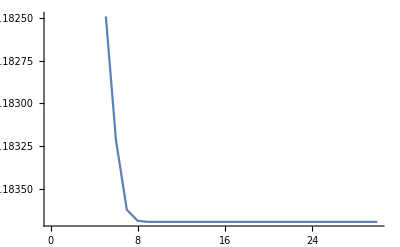

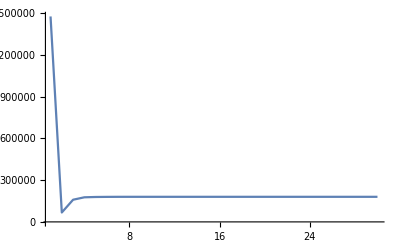

```mathematica
ListLinePlot[δe]
ListLinePlot[Flatten@EnergyCriteria,PlotRange->All]
```

```mathematica
MatrixForm[Flatten@EnergyCriteria]
```

(1.32777×10^6
75883.8
150077.
171054.
172717.
175820.
176686.
176768.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.
176787.)

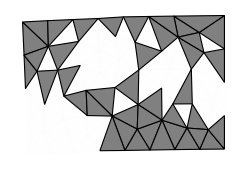

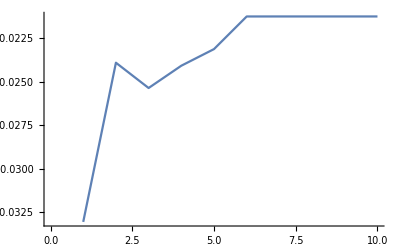

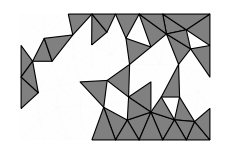

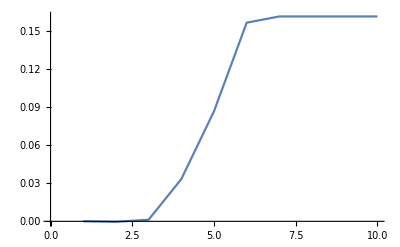

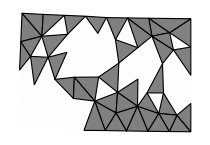

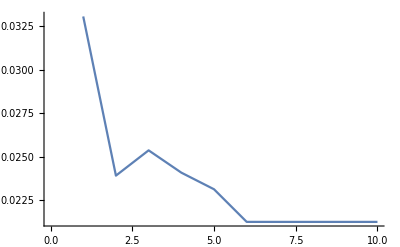

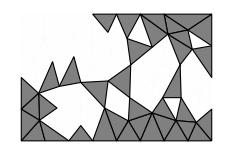

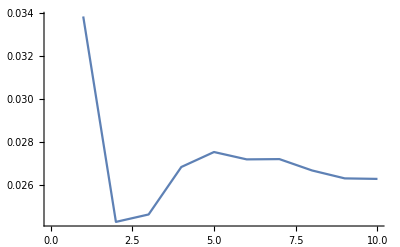

```mathematica
Sum[Transpose[ϝ[i]].Ke[i].ϝ[i],{i,1,Length[Polys]}]
```

{{176787.}}